# 📘Euler Method ✍️ Created by Haroon Sakhi

## ✨ Introduction

The Euler method is a numerical technique used to approximate the solutions of ordinary differential equations (ODEs) . Many real - world problems, involve differential equations that cannot be solved analytically . The Euler method provides an iterative approach to approximate the solution at discrete points .

### 🔢 Formula

where : 
📌 : Current function value
📌: Step size (determines step length)
📌 : Derivative at the current point
✔️ Smaller step sizes improve accuracy but increase computation time.

## 🛠️ Implementing Euler’s Method

Euler’s method follows these key steps:
🔹 Step 1: Convert the equation into the form   .
🔹 Step 2: Set the initial condition  .
🔹 Step 3: Choose a step size  and the number of steps.
🔹 Step 4: Iterate using Euler’s formula to compute -values.

## 📌 Example: Applying Euler’s Method

### 🔷 Defining the Differential Equation

```mathematica
dydx[x_]:=Cos[x]+1
Solution[x_]:=Sin[x]+x
```

✅ The exact solution is , which we compare against Euler’s approximation.

### 🔷 Writing the Euler Method Function

```mathematica
EulerMethod[xStart_, xEnd_, h_, (x0_ -> y0_)] := Module[{x, y, X, Y},
  X = {x0}; Y = {y0}; x = x0; y = y0;
  While[x < xEnd,
    x = x + h;
    y = y + h*dydx[x];
    AppendTo[X, x];
    AppendTo[Y, y];
  ];
  {X, Y}
]
```

#### 📍 Key Features :

🟢 Starts with initial values .

🔄 Iterates using Euler' s formula .

📊 Stores computed values for visualization .

### 🔷 Running the Method & Comparing with the Exact Solution

```mathematica
xStart = 0; xEnd = 5; h = 0.1;
{X, Y} = EulerMethod[xStart, xEnd, h, (0 -> 0)];
xSol = Subdivide[xStart, xEnd, 1000];
ySol = Solution /@ xSol;
```

#### 📍 Key Insights :

🔹 Step size: 0.1

🔹Comparison: Euler vs.exact solution

### 📊 Visualizing Results

#### 🟦 Euler Approximation vs. Exact Solution

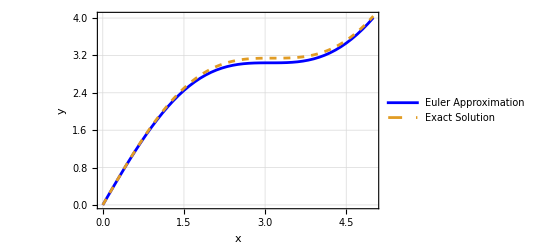

```mathematica
ListLinePlot[{
  Transpose[{X, Y}],
  Transpose[{xSol, ySol}]
  },
  PlotStyle -> {Blue, Dashed},
  PlotLegends -> {"Euler Approximation", "Exact Solution"},
  GridLines -> Automatic,
  Frame -> True,
  FrameLabel -> {"x", "y"},
  LabelStyle -> Directive[Bold, 12]
]
```

📌 Blue Line : Euler' s approximation
📌 Dashed Line : Exact solution
📌 Goal : Assess accuracy visually

## ⛔ Why Does Euler’s Method Fail?

Euler’s method doesn’t always work well, especially when the function changes rapidly or when a large step size is used. In such cases, the approximation can deviate significantly from the true solution. Let’s take a look at an example where Euler’s method struggles.

### 🔶 Example : Euler' s Method Fails

Consider the differential equation:

```mathematica
dydx[x_, y_] := -2*x*y
Solution[x_] := Exp[-x^2]
```

### 🔶 Implementing Euler’s Method

```mathematica
EulerMethod[start_, end_, dx_, {x0_, y0_}] := Module[{X, Y, x, y}, 
 X = {x0}; Y = {y0}; x = x0; y = y0;
  While[x < end, x = x + dx;
   y = y + dydx[x, y]*dx;
   AppendTo[X, x];
   AppendTo[Y, y];
   ];
  {X, Y}]
```

### 🔶 Running Euler’s Method and Comparing Results

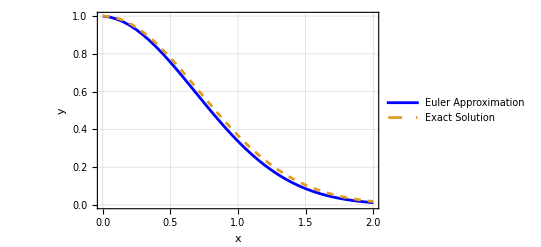

```mathematica
start = 0;
end= 2;
dx = 0.05;
{X, Y} = EulerMethod[start, end, dx, {0, 1}];

(* Compute exact solution for comparison *)
xSol = Subdivide[start, end, 1000];
ySol = Exp[-xSol^2];

(* Plot results *)
ListLinePlot[{Transpose[{X, Y}], Transpose[{xSol, ySol}]}, 
 PlotStyle -> {Blue, Dashed}, 
 PlotLegends -> {"Euler Approximation", "Exact Solution"}, 
 GridLines -> Automatic, Frame -> True, FrameLabel -> {"x", "y"}, 
 LabelStyle -> Directive[Bold, 14]]
```

### 🎛️ Making the Method Interactive

```mathematica
Manipulate[
  {X, Y} = EulerMethod[0, 2, dx, {0, 1}];
  ListLinePlot[{
    Transpose[{X, Y}],
    Transpose[{xSol, ySol}]
    },
    PlotStyle -> {Blue, Dashed},
    PlotLegends -> {"Euler Approximation", "Exact Solution"},
    GridLines -> Automatic,
    Frame -> True,
    FrameLabel -> {"x", "y"},
    LabelStyle -> Directive[Bold, 12]
  ],
  {dx, 0.1, 0.5, 0.01}
]
```

💡 Adjust  dynamically to observe how step size affects accuracy!

### 🔍 What Went Wrong?

📌 Euler’s method struggles because the function decreases rapidly, and the approximation lags behind the exact solution.
📌 The errors accumulate as we move forward, making the results unreliable.
📌 This highlights the need for more accurate methods, such as Runge-Kutta (RK4), which provides much better accuracy with similar computational effort.

## 🎯 Conclusion

✅ Euler’s method is simple and effective but accumulates errors.
🔬 Smaller step sizes yield better accuracy but increase computation.
🚀 Runge-Kutta methods offer improved precision over fewer steps.

## 🚀 Next Steps: In the next section, we’ll explore how Runge-Kutta (RK4) significantly improves accuracy over Euler’s method.